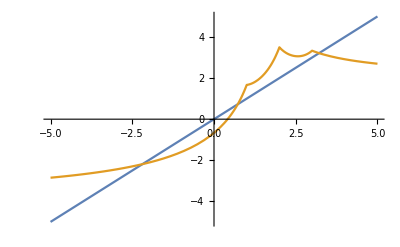

1.66667

3.5

3.33333

```mathematica
f[1]=1;
f[2]=2;
f[3]=3;
e=1;
ep=1;
g[x_]= ((x-f[3])+f[1])/(Abs[x-f[3]]^e+ep)+ ((x-f[1])+f[2])/(Abs[x-f[1]]^e +ep)+((x-f[2])+f[3])/(Abs[x-f[2]]^e+ep)-1;
Plot[{x,g[x]},{x,-5,5}]  
g[1.]
g[2.]
g[3.]
```

```mathematica
g[1]
```

3.41421

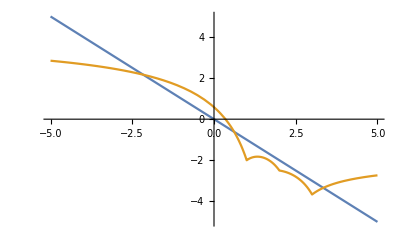

-2.

-2.5

-3.66667

```mathematica
f[1]=3;
f[2]=2;
f[3]=1;
e=1;
ep=1;
g[x_]:= -((x-f[3])+f[1])/(Abs[x-f[3]]^e+ep)-((x-f[1])+f[2])/(Abs[x-f[1]]^e +ep)-((x-f[2])+f[3])/(Abs[x-f[2]]^e+ep)+1;
Plot[{-x,g[x]},{x,-5,5}]  
g[1.]
g[2.]
g[3.]
```

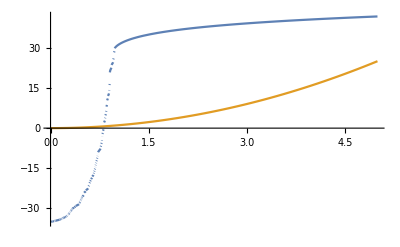

30.3972

36.8507

39.1241

```mathematica
f[x_]=x^2;
xx=Table[RandomReal[],{i,1,100}];
yy=f[xx];
g[x_]=Sum[yy[[i]]*(x-xx[[i]])/(Abs[x-xx[[i]]]^.9),{i,1,Length[xx]}];
Plot[{g[x],x^2},{x,0,5}]  
g[1.]
g[2.]
g[3.]
```